```mathematica
Reduce[Sqrt[250*c]>1/(3/10),c]
```

c>2/45

```mathematica
Reduce[Sqrt[250*c]>1/(0.3),c]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

c>0.0444444

```mathematica
2/45//N
```

0.0444444

```mathematica
Solve[0==(b-d)x(1-x/k)-a*x*y,y]
```

{{y→((b-d) (k-x))/(a k)}}

```mathematica
Solve[0==α*ϵ*x*y-m*y,y]
```

{{y→0}}

```mathematica
Solve[0==(b-d)x(1-x/k)-α*x*y&& 0==α*ϵ*x*y-m*y,{x,y}]
```

{{x→m/(α ϵ),y→((b-d) (-m+k α ϵ))/(k α^2 ϵ)},{x→0,y→0},{x→k,y→0}}

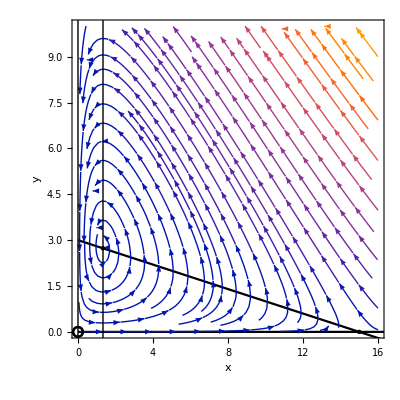

```mathematica
Show[{Plot[{((2-0.5) (15-x))/(0.5 15),0},{x,0,30},Epilog->{(*add vertical lines*)InfiniteLine[{0,0},{0,1}],InfiniteLine[{0.6/(0.9*0.5),0},{0,1}]},PlotStyle->Black,Frame->True,FrameLabel->{"x","y"}],ListPlot[List/@{{0.6/(0.5 0.9),((2-0.5) (-0.6+15 0.5 0.9))/(15 0.5^2 0.9)},{0,0},{15,0}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{None,{Graphics[Circle[]],Medium},None,{Graphics[Circle[]],Medium}}],StreamPlot[{(2-0.5)x(1-x/15)-0.5*x*y,0.5*0.9*x*y-0.6*y},{x,0,16},{y,0,10}]},PlotRange->{{0,16},{0,10}},AspectRatio->1]
```

```mathematica
ClearAll[x,y]
```

```mathematica
NDSolve[
x'[t]==(2-0.5)x[t](1-x[t]/15)-0.5*x[t]*y[t]&& 
y'[t]==0.5*0.9*x[t]*y[t]-0.6*y[t]&&
x[0]==10&&
y[0]==10,
{x,y},
{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

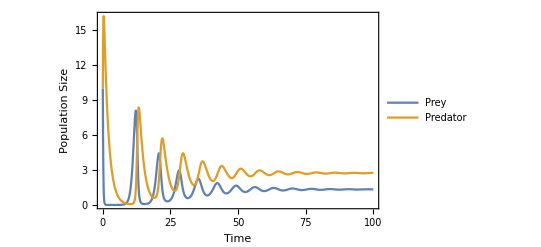

```mathematica
Plot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,100},PlotRange->All,Frame->True,FrameLabel->{"Time","Population Size"},PlotLegends->{"Prey","Predator"}]
```